```mathematica
(*Limit of Cayley distribution function*)
```

```mathematica
dC=Function[{k,r},Gamma[k+2]*(1+Cos[r])^k*(1-Cos[r])/(Sqrt[Pi]*2^(k+1)*Gamma[k+0.5])]
```

Function[{k,r},(Gamma[k+2] (1+Cos[r])^k (1-Cos[r]))/(√π 2^(k+1) Gamma[k+0.5])]

```mathematica
Limit[dC[k,r],k->0]
```

0.159155-0.159155 Cos[r]

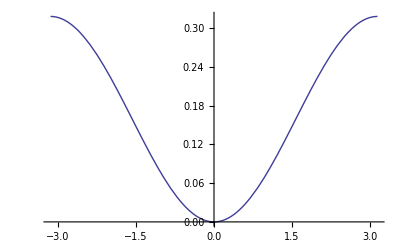

```mathematica
Plot[0.15915494309189532-0.15915494309189532 Cos[r],{r,-Pi,Pi}]
```

```mathematica
(*Limit of the matrix Fisher distribution*)
```

```mathematica
dF=Function[{k,r},Exp[2*k*Cos[r]]*(1-Cos[r])/(2*Pi*(BesselI[0,2*k]-BesselI[1,2*k]))]
```

Function[{k,r},(Exp[2 k Cos[r]] (1-Cos[r]))/(2 π (BesselI[0,2 k]-BesselI[1,2 k]))]

```mathematica
Limit[dF[k,r],k->0]
```

Sin[r/2]^2/π

```mathematica
Plot[Sin[r/2]^2/π,{r,-Pi,Pi}]
```

-Graphics-

```mathematica
N[1/(2*Pi)]
```

0.159155